# Probability and Statistics

### From Chapter 18 in Hands-On Start to Wolfram Mathematica - and Programming with the Wolfram Language Written by Cliff Hastings, Kelvin Mischo, Michael Morrison

Recreated with explanations in Mathematica by Sarah Sachs 🐺

## Probability and Distributions

Probability of rolling a three on a fair six-sided die

```mathematica
Probability[x==3,x\[Distributed]DiscreteUniformDistribution[{1,6}]]
```

1/6

Read this as: What is the probability that x = 3, if x is sampled from a discrete uniform distribution over the integers from 1 to 6?

first argument: describes the event (x==3)

second argument: distribution from which x is sampled

Distribution symbol \[Distributed] can be entered as Esc dist Esc on the keyboard

Join two events together
Example: Probability of obtaining a roll of 12 on two fair six-sided dice
	use && for And

```mathematica
Probability[x+y==12, x\[Distributed]DiscreteUniformDistribution[{1,6}]&& y\[Distributed]DiscreteUniformDistribution[{1,6}]]
```

1/36

List the probabilities for all the outcomes of rolling two dice. Keep in mind there are 11 possible results, from 2 to 12.

```mathematica
probs = Table[
Probability[x+y ==result,x\[Distributed]DiscreteUniformDistribution[{1,6}]&&y\[Distributed]DiscreteUniformDistribution[{1,6}]],
{result,2,12,1}]
```

{1/36,1/18,1/12,1/9,5/36,1/6,5/36,1/9,1/12,1/18,1/36}

Visualize this result using a BarChart

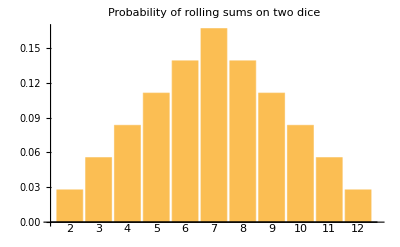

```mathematica
BarChart[probs,ChartLabels->Table[i,{i,2,12,1}],PlotLabel->"Probability of rolling sums on two dice"]
```

## Working with Distributions

Probability density function (PDF) used to show discrete uniform distribution shown earlier.

```mathematica
PDF[DiscreteUniformDistribution[{1,6}],x]
```

Piecewise[{{1/6, 1≤x≤6}, {0, True}}]

Use PDF to show normal distribution

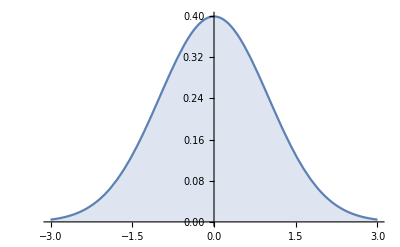

```mathematica
Plot[PDF[NormalDistribution[0,1],x],{x,-3,3},Filling->Axis]
```

## Creating Functions

Compute the values of the probability density function at certain points.

ex: create a function, myFun, based on the probability density function of the normal distribution with mean 0 and standard deviation 1

```mathematica
myFun[x_]:=PDF[NormalDistribution[0,1],x]
```

```mathematica
myFun[0]
```

1/(√(2 π))

You can also use functions in tables and manipulable objects

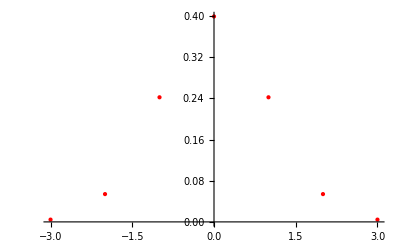

```mathematica
points = Table[{x,myFun[x]},{x,-3,3,1}];
ListPlot[points,PlotStyle->{Red,PointSize[Medium]}]
```

Use ; at the end of a command line if you want to suppress the output.

To make a plot using myFun to show both points and plot

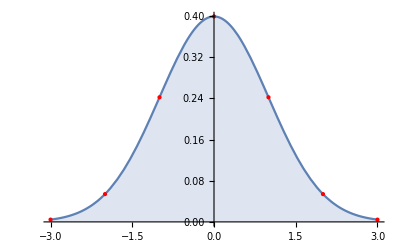

```mathematica
Show[
Plot[myFun[x],{x,-3,3},Filling->Axis],
ListPlot[points,PlotStyle->{Red,PointSize[Medium]}]]
```

Now to create a manipulable object

```mathematica
Manipulate[
Plot[PDF[NormalDistribution[μ,σ],x],{x,-3,3},Filling->Axis,PlotRange->{0,0.4}],
{μ,-2,2},{σ,1,4}]
```

## Statistics

### Descriptive Statistics

```mathematica
data={1,2,2,3,3,3,4,4,4,4,4,5,5,5,5,5,5};
```

```mathematica
Mean[data]
Median[data]
Commonest[data]
```

64/17

4

{5}

```mathematica
Variance[data]
StandardDeviation[data]
InterquartileRange[data]
```

213/136

(√(213/34))/2

2

Give two lists to find covariance and correlation

```mathematica
list1 ={1,1,1,2,2,2,2,3,3,3};
list2={1,2,2,3,3,4,4,5,5,5};
```

```mathematica
Covariance[list1,list2]
```

10/9

```mathematica
Correlation[list1,list2]
```

5 √(5/138)

### Curve Fitting

Construct models that find a fit and provide a framework for linear regression models.
Here is an example using data imported from Mathematica’s database.

Example: Iceland’s GDP from 1970 to 2010

```mathematica
myData=CountryData["Iceland",{{"GDP"},{1970,2017}}]
```

TimeSeries[…]

Data is returned as a TimeSeries object. We don’t need the temporal information in the dataset, so we can extract just the values using the “Values” property.

```mathematica
myData["Values"]
```

QuantityArray[…]

We don’t want the units, use the Quantity Magnitude function to discard the units and return just the values

```mathematica
QuantityMagnitude[myData["Values"]]
```

QuantityMagnitude[{5.31005×10^8,6.75723×10^8,8.46507×10^8,1.16386×10^9,1.52756×10^9,1.41836×10^9,1.68312×10^9,2.22654×10^9,2.53233×10^9,2.87673×10^9,3.40902×10^9,3.52151×10^9,3.2328×10^9,2.78853×10^9,2.88783×10^9,3.00841×10^9,4.02219×10^9,5.56538×10^9,6.15649×10^9,5.71888×10^9,6.52154×10^9,6.96614×10^9,7.13879×10^9,6.26935×10^9,6.44162×10^9,7.18179×10^9,7.50195×10^9,7.59613×10^9,8.46834×10^9,8.92819×10^9,8.92474×10^9,8.12616×10^9,9.1618×10^9,1.1297×10^10,1.37044×10^10,1.67493×10^10,1.70413×10^10,2.12938×10^10,1.75307×10^10,1.28553×10^10,1.32369×10^10}[Values]]

Now to visualize!

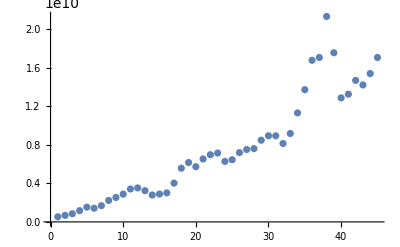

```mathematica
myData= QuantityMagnitude[myData["Values"]];
ListPlot[myData]
```

Use LinearModelFit to fit model, the arguments for this function are as listed:

LinearModelFit[dataset, {list of functions to construct a fit}, {variable of interest}]

```mathematica
myModel = LinearModelFit[myData,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8},x]
```

FittedModel[4.27393×10^9-4.79302×10^9 x+«9»+2.83205 x^8]

Use it like a univariate function, to evaluate at a certain value

```mathematica
myModel[1]
```

8.23834×10^8

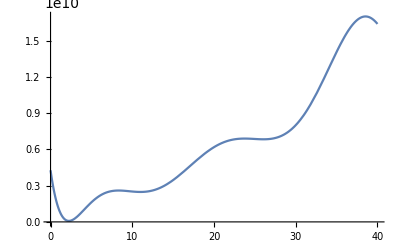

```mathematica
Plot[myModel[x],{x,0,40}]
```

Now superimpose this with the original dataset.

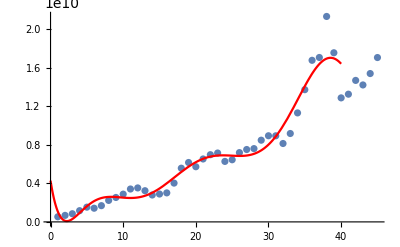

```mathematica
Show[
ListPlot[myData],
Plot[myModel[x],{x,0,40},PlotStyle->Red]
]
```

Many other properties are available. Use these to compute with the myModel. This is how you can see the full list:

```mathematica
Short[myModel["Properties"],10]
```

{AdjustedRSquared,AIC,AICc,ANOVATable,ANOVATableDegreesOfFreedom,ANOVATableEntries,ANOVATableFStatistics,ANOVATableMeanSquares,ANOVATablePValues,ANOVATableSumsOfSquares,BasisFunctions,BetaDifferences,BestFit,BestFitParameters,BIC,«34»,PartialSumOfSquares,PredictedResponse,Properties,Response,RSquared,SequentialSumOfSquares,SingleDeletionVariances,SinglePredictionBands,SinglePredictionConfidenceIntervals,SinglePredictionConfidenceIntervalTable,SinglePredictionConfidenceIntervalTableEntries,SinglePredictionErrors,StandardizedResiduals,StudentizedResiduals,VarianceInflationFactors}

```mathematica
myModel["AdjustedRSquared"]
```

0.943788

### Visualizing the Data

```mathematica
data={1,2,3,4,5};
GraphicsGrid[{
{BarChart[data],BarChart3D[data]},
{PieChart[data],PieChart3D[data]}
}]
```

-Graphics-

Ooooh aren’t these pretty...
Use special palettes to change the style of a chart. These can be found by clicking the Palettes menu and choosing Chart Element Schemes

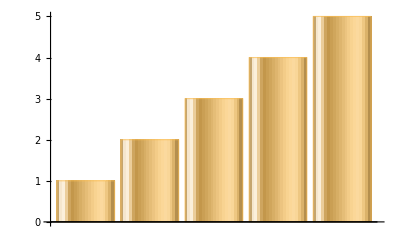

```mathematica
BarChart[data,ChartElementFunction->"GlassRectangle"]
```

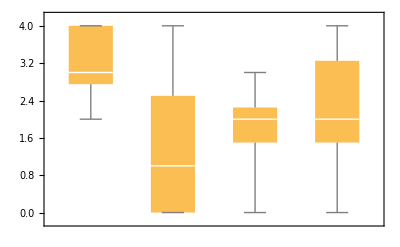

```mathematica
boxData = RandomInteger[{0,4},{4,5}];
BoxWhiskerChart[boxData]
```

Clear is used to remove all variables and function definitions that were created in this guide.

```mathematica
Clear[myFun,points,data,list1,list2,myData,myModel,boxData]
```